```mathematica
ClearAll["Global`*"]
```

Import Data

```mathematica
data = Import[StringJoin[{"[YOUR FILE PATH]/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{"[YOUR FILE PATH]/data/carnivoredensities_trimmed.csv"}],"csv"];
ppmrfitdata = Import[StringJoin[{"[YOUR FILE PATH]/data/ppmr_fit_table_revreps.csv"}],"csv"];
```

Define consumer-resource system and mass-dependent parameters

```mathematica
eqnC = λ*(R/(k/2+R))*C-( σ*(1-R/k)+μ+bP)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};
eqnR = α*R*(1-R/(k))-( λ/Y*(R/(k/2+R))+ρ)*C/.{k->kRes,λ->λ[M],Y->Y[M],μ->μ[M],ρ->ρ[M],σ->σ[M],bP->bP[M]};
LVSS = FullSimplify[Solve[{0==eqnC,0==eqnR},{C,R}]];
Csol = C/.LVSS[[4]]
Rsol = R/.LVSS[[4]]
```

-((α Y[M] (kRes (4 (bP[M]-λ[M]+μ[M])^2 (bP[M]+μ[M]+Y[M] ρ[M])+2 (5 bP[M]^2-5 bP[M] λ[M]+2 λ[M]^2+10 bP[M] μ[M]-5 λ[M] μ[M]+5 μ[M]^2+2 Y[M] (bP[M]+μ[M]) ρ[M]) σ[M]+(6 bP[M]-2 λ[M]+6 μ[M]+3 Y[M] ρ[M]) σ[M]^2)+2 bP[M]^2 √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 bP[M] λ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+4 bP[M] μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] μ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M]^2 √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 bP[M] Y[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 Y[M] λ[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 Y[M] μ[M] ρ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 bP[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-2 λ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))+2 μ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))-Y[M] ρ[M] σ[M] √(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2))))/(4 σ[M]^2 (2 (λ[M]+Y[M] ρ[M]) (bP[M]+μ[M]+Y[M] ρ[M])+(2 λ[M]+3 Y[M] ρ[M]) σ[M])))

(kRes (2 (bP[M]-λ[M]+μ[M])+σ[M])+√(kRes^2 (8 σ[M] (bP[M]+μ[M]+σ[M])+(2 (bP[M]-λ[M]+μ[M])+σ[M])^2)))/(4 σ[M])

Define metabolic parameters for herbivore consumer and resource

```mathematica
kRes=23000*(1+kMod);(*grams/m^2 carrying capacity of resource*)

Ed=18200; (*J/g of plant Resource *)
B0=4.7*10^(-2);(*W g^−0.75 for herbivores*)
Em=5774;(*J/gram - energy required to build gram of herbivore*)
a = B0/Em;

(*s=1;*)
Emprime =7000;
aprime =  B0/Emprime;
γ=1.19;
ζ=1.00;
f0=0.0202;
mm0=0.383;
α=(*2.10*10^(-9)*)(9.45*10^(-9)*(1+aMod));


τLam[M_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0[M]/M)^(1/4))]*(4*M^(1/4))/a;
λ[M_]:=(Log[2]/τLam[M]) (*Fecundity = 2*) (* max consumer growth rate of herbivore *)
BLam[M_]:=1/(3 a)ⅇ^(-(a τLam[M])/M^(1/4)) M^(1/4) (3 (-1+ⅇ^((a τLam[M])/M^(1/4))) m0[M]+M (-48 ⅇ^((3 a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))-36 ⅇ^((a τLam[M])/(2 M^(1/4))) (-1+(m0[M]/M)^(1/4))^2-16 ⅇ^((a τLam[M])/(4 M^(1/4))) (-1+(m0[M]/M)^(1/4))^3+3 (-1+4 (m0[M]/M)^(1/4)-6 √(m0[M]/M)+4 (m0[M]/M)^(3/4))+ⅇ^((a τLam[M])/M^(1/4)) (-25+12 (m0[M]/M)^(1/4)+6 √(m0[M]/M)+4 (m0[M]/M)^(3/4)))+3 a ⅇ^((a τLam[M])/M^(1/4)) M^(3/4) τLam[M]);
m0[M_]:=0.097*M^0.92;

(*k=(*10*)23000/2;*)
ρ[M_]:=B0*M^(η)/(M*Ed);
a0 = 1.88*10^-8 ;(*sec grams^-b0*)
a1=1.45*10^-7;
a2=4.04*10^6;
b0=-0.56;
b1=-0.27;
b2=0.30;
μ[M_] := (a0*(Exp[a1*a2*M^(b1+b2)]-1)*M^(b0-b1-b2))/(a1*a2)   (* this is the consumer death rate*)
(*STARVATION MORTALITY*)
ϵsig[M_] := (1-(f0*M^γ+mm0*M^ζ)/M);(*mortality from starvation state*)
τsig [M_]:=-M^(1/4)/aprime*Log[ϵsig[M]];(*time it takes to go from full to dead*)
σ[M_] := 1/τsig [M];(*starvation mortality rate)*)
```

Metabolic parameters for predator that eats herbivore consumer

```mathematica
η=3/4;
(*B0=4.7*10^(-2);(*W g^−0.75*)*)
B0Pred =(10^0.32)(*kJ/day*)*((0.01157(*Watts*))/(1(*kJ/day*))); (* in (kJ/d) for carnivora from https://doi.org/10.1086/432852 USING LOG10!!!!! *)
EmPred=5774;(*Energy to synthesize a unit of biomass not during starvation J/gram*)

aPred = B0Pred/EmPred;
m0Pred[Mp_]:=0.097*Mp^0.92;
ϵLam = 0.95;
τLamPred[Mp_]:= -Log[(1-ϵLam^(1/4))/(1 - (m0Pred[Mp]/Mp)^(1/4))]*(4*Mp^(1/4))/aPred;
λPred[Mp_]:=(Log[2]/τLamPred[Mp]) (*Fecundity = 2*) 
Bpred[Mp_]:=Integrate[(((1-(1-(m0Pred[Mp]/Mp)^(1/4))*E^(-aPred*t/(4*Mp^(1/4)))))^4)*Mp,{t,0,τLamPred[Mp]}]
```

Predator/prey interaction parameters

```mathematica
PredsperArea[Mp_] :=(0.000862119)*Mp^-0.88; (*Inds/m^2 w/ Mp (grams) From Carbone and Gittleman, Science 2002*)
PredDensity[Mp_] := Mp*PredsperArea[Mp]; (*grams/ind * inds/meter^2 = grams/m^2*)


(*--------------------*)
(*Optimal Predator mass given Prey (M) Mass*)
OptPredMass[M_]:=(1+κint)*ppmrint*M^(ppmrslope*(1+κslope));
ppmrslope = (ppmrfitdata[[3,1]]);
ppmrint = Exp[(ppmrfitdata[[2,1]])]*((1/1000)^ppmrslope)*1000; (*converted from KG to grams*)

(*Inverse: Optimal Prey mass given Predator (Mp) Mass*)
OptPreyMass[Mp_]:=Evaluate[M/.Solve[OptPredMass[M]==Mp,M][[1]]];

(*--------------------*)


OptPreypermeter2[Mp_] := 0.1156*OptPreyMass[Mp]^-0.77;
(*Damuth: Average Individuals/m2*)
OptPreygramspermeter2[Mp_] :=OptPreypermeter2[Mp]*OptPreyMass[Mp] ;
(*Average Individuals/m2 * average grams/individual*)
(*Percent fat + muscle*)
(*percentconsumable[M_]:=( 0.02*M^1.19 + 0.38*M^1.00)/M;*)
(*Or 1 - percent skeletal*)
massSkeletalgrams[M_]:= 0.0335*M^1.09263;
massFatgrams[M_]:=0.02*M^1.19;
massMusclegrams[M_]:=0.38*M^1.0;
massOthergrams[M_]:=M-(massSkeletalgrams[M]+massFatgrams[M]+massMusclegrams[M]);
(*This is nearly 100% from Prange et al. AmNat 1979*)
(*Energy Density of PREY Joules/gram*)
(*BLUBBER energy content 37670 J/gram SAME AS FAT *)
(*NOTE: THINK CAREFULLY ABOUT THIS *)
FatJperG = 37700;
ProteinJperG = 17900;
MuscleJperG = 0.4*ProteinJperG + 0.6*FatJperG;
(*TissueJperG = ProteinJperG+FatJperG;
PercentFat =(FatJperG/TissueJperG);
PercentProtein =(1- PercentFat);*)
Eprey[M_]:=(1/(M))*(massFatgrams[M]*FatJperG+massMusclegrams[M]*MuscleJperG+massOthergrams[M]*MuscleJperG);
(*Eprey[M_,ϵEprey_] := ((PercentProtein*TissueJperG)+(PercentFat*TissueJperG)+0)*(1+ϵEprey)*percentconsumable[M];*)
(*Joules/gram: 17000 protein + 37000 fat + 0 carb per gram of meat http://www.fao.org/3/y5022e/y5022e04.htm  Modified from Merrill and Watt (1973).*)
(*Results of MAXSIZE are very sensitive to Energy Density of Prey*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Calculate Herbivore Yield

```mathematica
YHerbperRes[M_]:=M*Ed/BLam[M]; (*Grams herb / Grams Resource given the mass of an Herbivore*)
Y[M_]:=YHerbperRes[M];
(*kprey[Mp_]:=OptPreygramspermeter2[Mp]; *)(*PREY carrying capacity grams/m^2*)
```

Calculate Predator Yield

```mathematica
(*Yield of predator per prey*)
Ypred[Mp_,M_] := (Mp*Eprey[M])/Bpred[Mp]; (*Grams of predator per grams of prey*)
```

Calculate Consumer and Predator Boundary Densities

```mathematica
PreyDensityTheoreticalMax[M_] := YHerbperRes[M]*kRes; (*Grams Herb / m^2 given the mass of a predator and the optimal prey mass given predator mass conversion*)
PreyDensityTheoreticalHalfSat[M_]:=(PreyDensityTheoreticalMax[M]*(1-χ))/χ/.χ->0.99;
PredatorDensityTheoreticalMax[Mp_,M_]:=Ypred[Mp,M]*YHerbperRes[M]*kRes;
```

Calculate per-capita Predation Mortality Rate as (predation rate per gram consumer)*(predated consumer density)

```mathematica
predgrowthrateperconsumer[Mp_,M_] :=λPred[Mp]/PreyDensityTheoreticalMax[M];
predatedconsumerdensity[Mp_,M_]:=PredDensity[Mp]/Ypred[Mp,M];
(*predrate[Mp_,M_,ϵEprey_] := (λPred[Mp]*PredDensity[Mp])/PredDensityMaxPreyGrowth[Mp,M,ϵEprey](*((1/time)*gpred/m^2)/(gpred/m^2)=1/time*);*)
predmortality = FullSimplify[w*predgrowthrateperconsumer[Mp,M]*predatedconsumerdensity[Mp,M]];
predmortalityfull[Mp_,M_]:=  Evaluate[predmortality//Simplify];

bP[M_] :=predmortalityfull[OptPredMass[M],M];
```

Examine the effect of known variability in the resource growth rate and carrying capacities for terrestrial grasses/shrubs/trees without predation (w=0)

{{minmod→-0.970265}}

{{maxmod→1.31746}}

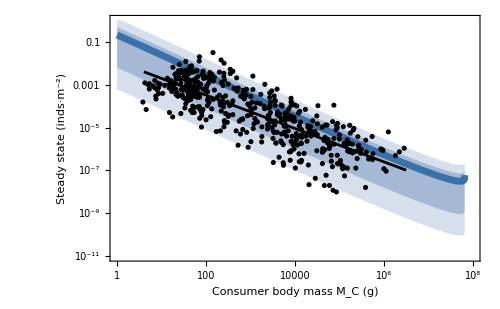

```mathematica
minmodsol = Solve[2.81*10^-10==((9.45*10^(-9))*(1+minmod)),minmod]
maxmodsol=Solve[2.19*10^-8==((9.45*10^(-9))*(1+maxmod)),maxmod]
ConsumerDensityResourcePlot = Show[{
LogLogPlot[
{(1/M)*Csol/.{aMod->0,kMod->0,w->0},
(1/M)*Csol/.{(aMod->maxmod/.maxmodsol)[[1]],kMod->0,κint->0,κslope->0,w->0},(1/M)*Csol/.{(aMod->minmod/.minmodsol)[[1]],kMod->0,κint->0,κslope->0,w->0},
(1/M)*Csol/.{(aMod->minmod/.minmodsol)[[1]],kMod->-0.9,κint->0,κslope->0,w->0},
(1/M)*Csol/.{(aMod->maxmod/.maxmodsol)[[1]],kMod->1.5,κint->0,κslope->0,w->0}},{M,1,1*10^8},PlotStyle->{ColorData[97,1],Transparent,Transparent,Transparent,Transparent},Filling->{
3->{{2},Directive[ColorData[97,1],Opacity[0.4]]},5->{{4},Directive[ColorData[97,1],Opacity[0.25]]}
},PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Consumer body mass M_C (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
LogLogPlot[
(1/M)*Csol/.{aMod->0,kMod->0,κint->0,κslope->0,w->0},{M,1,1*10^8},PlotStyle->Directive[ColorData[91,1],Thickness[0.01]]],
ListLogLogPlot[data,PlotStyle->Black],
LogLogPlot[Exp[-4.459834805724913]*x^-0.7768181657741381,{x,4,10^6.5},PlotStyle->Directive[Black]]
},ImageSize->500]
```

With predator mortality (w=1), find mass thresholds as a function of changes to carrying capacity (kMod)

```mathematica
CarryingCapacityThreshold = ParallelTable[Quiet[{N[(M/.FindMinimum[Abs[(1/M)*Csol/.{κint->0,κslope->0,aMod->0,kMod->i,w->1}],M][[2]])],i}],{i,-0.2,0.2,0.01}];
```

```mathematica
CenterMass=N[(M/.FindMinimum[Abs[(1/M)*Csol/.{κint->0,κslope->0,aMod->0,kMod->0,w->1}],M][[2]])]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

2.54997×10^6

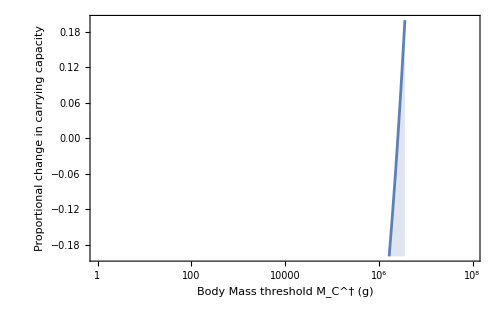

```mathematica
CarryingCapacityPlot = ListLogLinearPlot[CarryingCapacityThreshold,PlotRange->{{10^0,10^8},{-0.2,0.2}},Joined->True,Frame->True,FrameLabel->{"Body Mass threshold M_C^† (g)","Proportional change in carrying capacity"},LabelStyle->Directive[FontSize->16],ImageSize->500, Filling->Bottom]
```

```mathematica
Export[StringJoin[{"[YOUR FILE PATH]/fig_carryingcapacity_threshold.pdf"}],CarryingCapacityPlot,"PDF"]
```

Define Jacobian for the consumer resource system

```mathematica
JacobianFullModel=(({
{D[eqnC,C],D[eqnC,R]},
{D[eqnR,C],D[eqnR,R]}})/.{C->Csol,R->Rsol})/.{κint->0,κslope->0,aMod->0,kMod->0,w->1};
```

Quantify eigenvalues as a function of consumer mass

```mathematica
EigList = Table[Flatten[{10^i,Re[Eigenvalues[JacobianFullModel/.M->10^i]]},1],{i,0,8,0.05}];
```

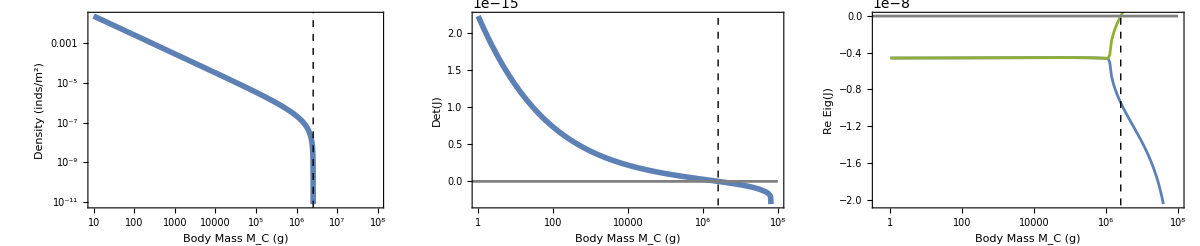

```mathematica
StabilityPlot = GraphicsRow[{
Show[{
LogLogPlot[(1/M)*Csol/.{κint->0,κslope->0,aMod->0,kMod->0,w->1},{M,10,10^8},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,1]},FrameLabel->{"Body Mass M_C (g)","Density (inds/m^2)"},LabelStyle->Directive[FontSize->16],ImageSize->500],
Graphics[{Black,Thick,Dashed,Line[{{Log@(CenterMass),Log@(10^-12)},{Log@(CenterMass),Log@(1)}}]}]
}],
Show[{
LogLinearPlot[Det[JacobianFullModel],{M,1,10^8},Frame->True,PlotStyle->{Thickness[0.008],ColorData[97,1]},FrameLabel->{"Body Mass M_C (g)","Det(J)"},LabelStyle->Directive[FontSize->16],ImageSize->500],
Graphics[{Black,Thick,Dashed,Line[{{Log@(CenterMass),-1},{Log@(CenterMass),1+1}}]}],
LogLinearPlot[0,{M,0.1,10^8},PlotStyle->Gray]
}],
Show[{
ListLogLinearPlot[Transpose[{EigList[[All,1]],EigList[[All,2]]}],Joined->True,Frame->True,FrameLabel->{"Body Mass M_C (g)","Re Eig(J)"},LabelStyle->Directive[FontSize->16],ImageSize->500],
ListLogLinearPlot[Transpose[{EigList[[All,1]],EigList[[All,3]]}],Joined->True,PlotStyle->ColorData[97,3]],
Graphics[{Black,Thick,Dashed,Line[{{Log@(CenterMass),-1},{Log@(CenterMass),1+1}}]}],
LogLinearPlot[0,{M,0.1,10^8},PlotStyle->Gray]
}]
},ImageSize->1200,Spacings->0.8]
```

```mathematica
Export[StringJoin[{"[YOUR FILE PATH]/fig_stability.pdf"}],StabilityPlot,"PDF"]
```